```mathematica
PP={{1-p,p,0,0,0},{p-p^2,2*p^2-2*p+1,p-p^2,0,0},{0,p-p^2,2*p^2-2*p+1,p-p^2,0},{0,0,p-p^2,2*p^2-2*p+1,p-p^2},{0,0,0,p*(1-p),1-p*(1-p)}}
```

{{1-p,p,0,0,0},{p-p^2,1-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,1-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,1-2 p+2 p^2,p-p^2},{0,0,0,(1-p) p,1-(1-p) p}}

```mathematica
MatrixForm[PP]
```

(1-p | p | 0 | 0 | 0
p-p^2 | 1-2 p+2 p^2 | p-p^2 | 0 | 0
0 | p-p^2 | 1-2 p+2 p^2 | p-p^2 | 0
0 | 0 | p-p^2 | 1-2 p+2 p^2 | p-p^2
0 | 0 | 0 | (1-p) p | 1-(1-p) p)

```mathematica
MatrixForm[P]
```

(1-p | p | 0 | 0 | 0
p-p^2 | 1-2 p+2 p^2 | p-p^2 | 0 | 0
0 | p-p^2 | 1-2 p+2 p^2 | p-p^2 | 0
0 | 0 | p-p^2 | 1-2 p+2 p^2 | p-p^2
0 | 0 | 0 | p | 1-p)

```mathematica
P1=Transpose[P]-IdentityMatrix[5]
```

{{-p,p-p^2,0,0,0},{p,-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,-2 p+2 p^2,p},{0,0,0,p-p^2,-p}}

```mathematica
MatrixForm[%]
```

(-p | p-p^2 | 0 | 0 | 0
p | -2 p+2 p^2 | p-p^2 | 0 | 0
0 | p-p^2 | -2 p+2 p^2 | p-p^2 | 0
0 | 0 | p-p^2 | -2 p+2 p^2 | p
0 | 0 | 0 | p-p^2 | -p)

```mathematica
Det[{{-p,p-p^2,0,0,0},{p,-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,-2 p+2 p^2,p},{0,0,0,p-p^2,-p}}]
```

0

```mathematica
Assuming[1>p>0,NullSpace[P1]]
```

{{1,-1/(-1+p),-1/(-1+p),-1/(-1+p),1}}

```mathematica
MatrixForm[{{1,-1/(-1+p),-1/(-1+p),-1/(-1+p),1}}]
```

(1 | -1/(-1+p) | -1/(-1+p) | -1/(-1+p) | 1)

```mathematica
25*5
```

125

```mathematica
36*6
```

216

```mathematica
1-125/216
```

91/216

```mathematica
1+3*25*16/(36*11)+3*5/36
```

587/132

```mathematica
1+%
```

719/132

```mathematica
%/(91/216)
```

12942/1001

```mathematica
5^4/6^4
```

625/1296

```mathematica
E3=12942/1001
```

12942/1001

```mathematica
E2=
```

```mathematica
96/11
```

96/11

```mathematica
E2=%
```

96/11

```mathematica
E1=6
```

6

```mathematica
(1+4*(5^3)*E3/6^4+6*(5^2)/(6^4)*E2+4*5/6^4)/(1-(5^4/6^4))
```

75196/5551

```mathematica
E4=%
```

75196/5551

```mathematica
(1+5*E4*5^4/6^5+10*(5/6)^3*(1/6)^2*E3+10*(5/6)^2*(1/6)^3*E2+5(5/6)*(1/6)^4*E1)/(1-(5/6)^5)
```

4188883486/283994711

```mathematica
N[4188883486/283994711]
```

14.7499

```mathematica
5^4
```

625

```mathematica
625*5
```

3125

```mathematica
P={{5^5/6^5,3125/6^5,1250/6^5,250/6^5,25/6^5},{0,625/6^4,500/6^4,150/6^4,20/6^4},{0,0,125/6^3,75/6^3,15/6^3},{0,0,0,25/6^2,10/6^2},{0,0,0,0,5/6}}
```

{{3125/7776,3125/7776,625/3888,125/3888,25/7776},{0,625/1296,125/324,25/216,5/324},{0,0,125/216,25/72,5/72},{0,0,0,25/36,5/18},{0,0,0,0,5/6}}

```mathematica
MatrixForm[P]
```

(3125/7776 | 3125/7776 | 625/3888 | 125/3888 | 25/7776
0 | 625/1296 | 125/324 | 25/216 | 5/324
0 | 0 | 125/216 | 25/72 | 5/72
0 | 0 | 0 | 25/36 | 5/18
0 | 0 | 0 | 0 | 5/6)

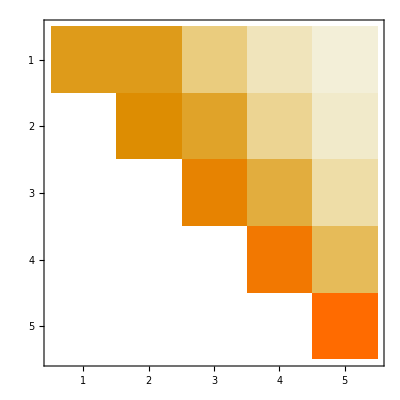

```mathematica
MatrixPlot[P]
```

```mathematica
MatrixForm[P]
```

(3125/46656 | 3125/7776 | 625/3888 | 125/3888 | 25/7776
0 | 625/1296 | 125/324 | 25/216 | 5/324
0 | 0 | 125/216 | 25/72 | 5/72
0 | 0 | 0 | 25/36 | 5/18
0 | 0 | 0 | 0 | 5/6)

```mathematica
{{3125/46656,3125/7776,625/3888,125/3888,25/7776},{0,625/1296,125/324,25/216,5/324},{0,0,125/216,25/72,5/72},{0,0,0,25/36},{0,0,0,0,5/6}}
```

```mathematica
P=%
```

{{3125/46656,3125/7776,625/3888,125/3888,25/7776},{0,625/1296,125/324,25/216,5/324},{0,0,125/216,25/72,5/72},{0,0,0,25/36},{0,0,0,0,5/6}}

```mathematica
NullSpace[m,Transpose[{1,1,1,1,1}]]
```

Transpose::nmtx: The first two levels of {1,1,1,1,1} cannot be transposed.

NullSpace::nonopt: Options expected (instead of Transpose[{1,1,1,1,1}]) beyond position 1 in NullSpace[m,Transpose[{1,1,1,1,1}]]. An option must be a rule or a list of rules.

```mathematica
NullSpace[m,{{1},{1},{1},{1},{1}}]
```

NullSpace::nonopt: Options expected (instead of {{1},{1},{1},{1},{1}}) beyond position 1 in NullSpace[m,{{1},{1},{1},{1},{1}}]. An option must be a rule or a list of rules.

NullSpace[m,{{1},{1},{1},{1},{1}}]

```mathematica
{1,1,1,1,1}
```

{1,1,1,1,1}

```mathematica
LinearSolve[IdentityMatrix[5]-P,{{1},{1},{1},{1},{1}}]
```

{{3698650986/283994711},{728256/61061},{10566/1001},{96/11},{6}}

```mathematica
Grid[{{3698650986/283994711},{728256/61061},{10566/1001},{96/11},{6}}]
```

3698650986/283994711
728256/61061
10566/1001
96/11
6

```mathematica
3698650986/283994711
```

3698650986/283994711

```mathematica
N[3698650986/283994711]
```

13.0237

```mathematica
PP
```

{{1-p,p,0,0,0},{p-p^2,1-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,1-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,1-2 p+2 p^2,p-p^2},{0,0,0,(1-p) p,1-(1-p) p}}

```mathematica
Assuming[{1>p>0},NullSpace[Transpose[PP]-IdentityMatrix[5]]]
```

{{1-p,1,1,1,1}}

```mathematica
F1=Assuming[{{k ∈ Ν },{k>0}},Array[p*(1-p),k]
```

```mathematica
F1
```

Array[(1-p) p,k]

```mathematica
Assuming[{{k ∈ Ν },{k>0}},DiagonalMatrix[F1]]
```

DiagonalMatrix[Array[(1-p) p,k]]

```mathematica
PP
```

{{1-p,p,0,0,0},{p-p^2,1-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,1-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,1-2 p+2 p^2,p-p^2},{0,0,0,(1-p) p,1-(1-p) p}}

```mathematica
MatrixForm[PP]
```

(1-p | p | 0 | 0 | 0
p-p^2 | 1-2 p+2 p^2 | p-p^2 | 0 | 0
0 | p-p^2 | 1-2 p+2 p^2 | p-p^2 | 0
0 | 0 | p-p^2 | 1-2 p+2 p^2 | p-p^2
0 | 0 | 0 | (1-p) p | 1-(1-p) p)

```mathematica
MatrixForm[Transpose[PP]-IdentityMatrix[5]]
```

(-p | p-p^2 | 0 | 0 | 0
p | -2 p+2 p^2 | p-p^2 | 0 | 0
0 | p-p^2 | -2 p+2 p^2 | p-p^2 | 0
0 | 0 | p-p^2 | -2 p+2 p^2 | (1-p) p
0 | 0 | 0 | p-p^2 | -(1-p) p)

```mathematica
Dimensions[{{-p,p-p^2,0,0,0},{p,-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,-2 p+2 p^2,(1-p) p},{0,0,0,p-p^2,-(1-p) p}}]
```

{5,5}

```mathematica
Det[{{-p,p-p^2,0,0,0},{p,-2 p+2 p^2,p-p^2,0,0},{0,p-p^2,-2 p+2 p^2,p-p^2,0},{0,0,p-p^2,-2 p+2 p^2,(1-p) p},{0,0,0,p-p^2,-(1-p) p}}]
```

0

```mathematica
P4={{1,0,0,0,0,0},{1/6,-1,5/6,0,0,0},{0,1/2,-1,1/2,0,0},{0,1/2,0,-1,1/2,0},{0,1/2,0,0,-1,1/2},{0,0,0,0,0,1}}
```

{{1,0,0,0,0,0},{1/6,-1,5/6,0,0,0},{0,1/2,-1,1/2,0,0},{0,1/2,0,-1,1/2,0},{0,1/2,0,0,-1,1/2},{0,0,0,0,0,1}}

```mathematica
MatrixForm[P4]
```

(1 | 0 | 0 | 0 | 0 | 0
1/6 | -1 | 5/6 | 0 | 0 | 0
0 | 1/2 | -1 | 1/2 | 0 | 0
0 | 1/2 | 0 | -1 | 1/2 | 0
0 | 1/2 | 0 | 0 | -1 | 1/2
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
LinearSolve[P4,{0,0,0,0,0,1}]
```

{0,5/13,6/13,7/13,9/13,1}

```mathematica
LinearSolve[P4,-{0,1,1,1,1,0}]
```

{0,118/13,126/13,108/13,72/13,0}

```mathematica
P1C={{0,1/2,1/2},{1/4,1/2,1/4},{1/4,1/4,1/2}}
```

{{0,1/2,1/2},{1/4,1/2,1/4},{1/4,1/4,1/2}}

```mathematica
Grid[P1C]
```

0 | 1/2 | 1/2
1/4 | 1/2 | 1/4
1/4 | 1/4 | 1/2

```mathematica
MatrixForm[P1C]
```

(0 | 1/2 | 1/2
1/4 | 1/2 | 1/4
1/4 | 1/4 | 1/2)

```mathematica
NullSpace[Transpose[P1C]-IdentityMatrix[3]]
```

{{1/2,1,1}}